```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

PacletObject[…]

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/opt/homebrew/bin/pdflatex","Ghostscript"->"/opt/homebrew/bin/gs"
]*)
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→/opt/homebrew/bin/pdflatex,Ghostscript→/opt/homebrew/bin/gs}

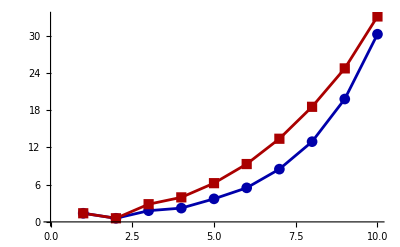

p2.jpeg

p3.jpeg

p_all.jpeg

```mathematica
ClearAll[alpha, beta, a,b]

SetDirectory["~/tmp"];
data=Import["data.json"];

ClearAll[plotOnePair]
plotOnePair[element_, onePlot_]:=Module[{test,pred,alpha,beta,a,b, defaultOptions, onePlotOptions, manyPlotOptions},
a=Lookup[element,"a"];
b=Lookup[element,"b"];
alpha=Lookup[element,"alpha"];
beta=Lookup[element,"beta"];
test=Lookup[element,"test_sequence"];
pred=Lookup[element,"predictions"];

defaultOptions = {
PlotMarkers->Automatic,
PlotStyle->{Blue// Darker,Red//Darker}
};

onePlotOptions=
{PlotLegends-> Placed[({"\\color{BlueDarker}\\mathrm{\\mbox{Test Sequence}}","\\color{RedDarker}\\mathrm{\\mbox{Predictions}}"} // MaTeX), {Left,Top}],
PlotLabel->MaTeX[StringForm["\\alpha = ``, \\beta = ``, a = ``, b = ``",alpha,beta,a,b]]
(*,
AxesLabel->({"Index","Value"}//MaTeX)*)
};

manyPlotOptions = {
Ticks -> None
};

ListLinePlot[{test,pred},Sequence@@If[onePlot,Join[defaultOptions, onePlotOptions],Join[defaultOptions,manyPlotOptions]]
]
]


ClearAll[p2, p3, pall]
p2 = plotOnePair[data[[2]], True];
p3  = plotOnePair[data[[3]], True]
pall = GraphicsGrid[Partition[plotOnePair[#, False]&/@ data,UpTo[4]]];

Export["p2.jpeg", p2]
Export["p3.jpeg", p3]
Export["p_all.jpeg", pall]
```